```mathematica
a1={1/2,1/2,0}
a2={1/2,0,1/2}
a3={0,1/2,1/2}
```

{1/2,1/2,0}

{1/2,0,1/2}

{0,1/2,1/2}

```mathematica
Cross[a1,a2].a3
```

-1/4

```mathematica
Cross[a2,a1].a3
```

1/4

```mathematica
Cross[a1,a2]
```

{1/4,-1/4,-1/4}

```mathematica
Dot[a1,Times[a2,a3]]
```

```mathematica
p=Parallelepiped[{0,0,0},{a1,a2,a3}]
```

Parallelepiped[{0,0,0},{{1/2,1/2,0},{1/2,0,1/2},{0,1/2,1/2}}]

```mathematica
o={0,0,0};
```

```mathematica
Show[Graphics3D[p],Graphics3D[Arrow[{o,#}]&/@{a1,a2,a3}]]
```

-Graphics3D-

```mathematica
c=BoundingRegion[p,"MinCuboid"]
```

Cuboid[{0,0,0},{1,1,1}]

```mathematica
Show[Graphics3D[{p,{Opacity[0.4],c}}],Graphics3D[Arrow[{o,#}]&/@{a1,a2,a3}]]
```

-Graphics3D-

```mathematica
Volume[p]
```

1/4

```mathematica
Volume[c]
```

1

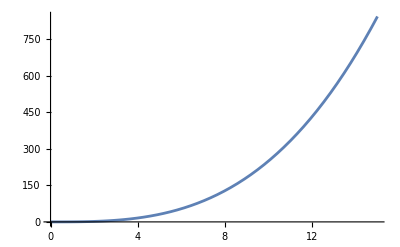

```mathematica
Plot[Volume[Parallelepiped[{0,0,0},x{a1,a2,a3}]],{x,0,15}]
```

```mathematica
NSolve[Volume[Parallelepiped[{0,0,0},x{a1,a2,a3}]]==]
```

```mathematica
g=Parallelepiped[{0,0,0},{a1,a2,a3}]
```

```mathematica
NSolve[x^3/4==7.44(Quantity[, ("Nanometers")^3]/10^3),x]
```

{{x→(-1.54946×10^-10-2.68375×10^-10 ⅈ) m},{x→(-1.54946×10^-10+2.68375×10^-10 ⅈ) m},{x→3.09892×10^-10 m}}

```mathematica
UnitConvert[1,"A"]
```

```mathematica
r1={1,-3,2};
r2={3,7,-5};
r3={4,1,6};
Dot[r1,Times[r2,r3]]
```

-69

```mathematica
r1.r2
```

-28

```mathematica
r1.Times[r2,r3]
```

-69

```mathematica
LatticeData["FaceCenteredCubic","Image"]
```

-Graphics3D-

```mathematica
dat2=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/out.txt","Table"]//Flatten;
dat2=dat2[[1;;All]]
```

{-4.68168,-4.6053,-4.65265,-4.65816,-4.67631,-4.66799,-4.67297,-4.66575,-4.66554,-4.66491,-4.66607,-4.6673,-4.66904,-4.66788,-4.66774,-4.66702,-4.66776,-4.66708,-4.66771,-4.66752,-4.66797,-4.66791,-4.66771,-4.66745,-4.66755,-4.6676}

```mathematica
Length@dat2
```

26

```mathematica
Range[5,40,1]//Length
```

36

```mathematica
3
```

```mathematica
dattr2=Transpose[{Range[5,30,1],dat2}];
```

```mathematica
fnfit2=Interpolation[dattr2,Method->"Spline",InterpolationOrder->6]
```

InterpolatingFunction[…]

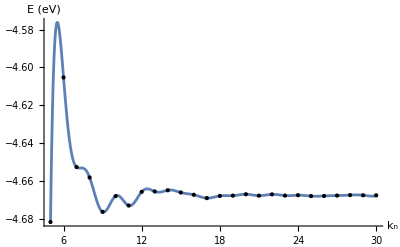

```mathematica
plt2=Plot[fnfit2[x],{x,5,30},Epilog->{Point[dattr2]},PlotRange->All,AxesLabel->{"k_n","E (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltK.pdf",plt2]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltK.pdf

{0.0763781,0.0473501,0.00550627,0.0181534,0.00832443,0.0049803,0.00721538,0.00021025,0.00062961,0.00116129,0.00122901,0.00173432,0.00115368,0.00013909,0.0007279,0.00073919,0.00067618,0.00062695,0.00019055,0.0004555,0.00006615,0.00019341,0.00026694,0.00010424,0.0000468}

25

{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

25

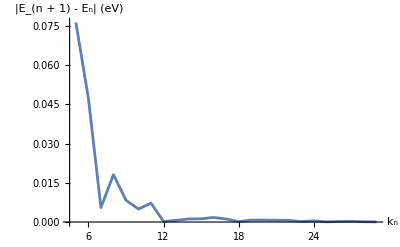

```mathematica
f=Abs@Differences[dat2]
Length@f
Range[5,29]
Length@Range[5,29]
kpltConv=ListLinePlot[Transpose[{Range[5,29],f}],PlotRange->All,AxesLabel->{"k_n","|E_(n + 1) - E_n| (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/kpltConv.pdf",kpltConv]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/kpltConv.pdf

## Volume values

```mathematica
Around[7.44,0.2 7.44]
vint=Subdivide[7.44-1.5,7.44+1.5,25]
```

7.41.5

{5.94,6.06,6.18,6.3,6.42,6.54,6.66,6.78,6.9,7.02,7.14,7.26,7.38,7.5,7.62,7.74,7.86,7.98,8.1,8.22,8.34,8.46,8.58,8.7,8.82,8.94}

```mathematica
Lengt@vint
```

Lengt[{5.94,6.06,6.18,6.3,6.42,6.54,6.66,6.78,6.9,7.02,7.14,7.26,7.38,7.5,7.62,7.74,7.86,7.98,8.1,8.22,8.34,8.46,8.58,8.7,8.82,8.94}]

```mathematica
step=3/25//N
```

0.12

```mathematica
avals=NSolveValues[a^3/4==#,a][[3]]&/@vint
```

{2.87485,2.89408,2.91306,2.93179,2.95029,2.96856,2.98661,3.00444,3.02206,3.03948,3.0567,3.07373,3.09057,3.10723,3.12372,3.14003,3.15617,3.17215,3.18798,3.20364,3.21916,3.23452,3.24974,3.26482,3.27977,3.29457}

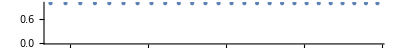

```mathematica
NumberLinePlot[avals]
```

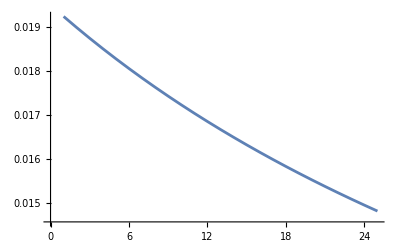

```mathematica
Differences[avals]//ListLinePlot
```

```mathematica
ToString@StringForm["`` ",#]&/@avals//StringJoin
```

2.87485 2.89408 2.91306 2.93179 2.95029 2.96856 2.98661 3.00444 3.02206 3.03948 3.0567 3.07373 3.09057 3.10723 3.12372 3.14003 3.15617 3.17215 3.18798 3.20364 3.21916 3.23452 3.24974 3.26482 3.27977 3.29457

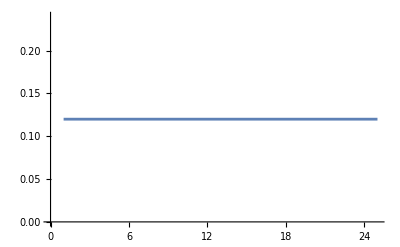

```mathematica
Differences[vint]//ListLinePlot
```

## FCC DOS

```mathematica
fccdos=Import[","]
```

Import::nffil: File , not found during Import.

$Failed

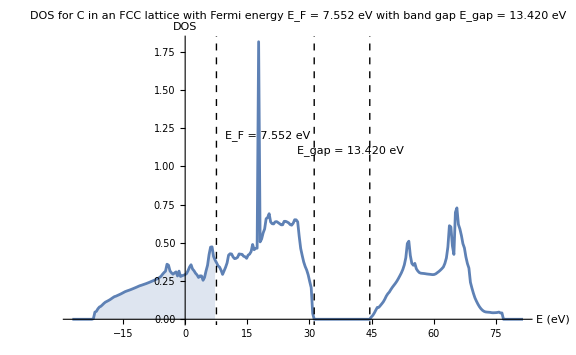

```mathematica
doscs=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/FCC/DOSCAR","Table","HeaderLines"->6];
cc2={#1,#2}&@@@doscs;

dosc2=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/FCC/DOSCAR2","Table","HeaderLines"->6];
dosc2a={#1,#2}&@@@dosc2;
dplot=Show[ListLinePlot[{cc2+dosc2a},PlotRange->All,ImageSize->Medium,AxesLabel->{"E (eV)","DOS"},Epilog->{Dashed,Line[{{7.552,-3},{7.552,3}}],Text["E_F = 7.552 eV",{20,1.2}],Line[{{31.162,-3},{31.162,3}}],Line[{{44.582,-3},{44.582,3}}],Text["E_gap = 13.420 eV",{40,1.1}]},PlotLabel->"DOS for C in an FCC lattice with Fermi energy E_F = 7.552 eV with band gap E_gap = 13.420 eV"],ListLinePlot[Select[cc2+dosc2a,#[[1]]<=7.552&],Filling->Axis,PlotStyle->Directive[RGBColor[0,0,0,0.0]]],ImageSize->Large]
```

```mathematica
Select[cc2+dosc2a,0<#[[1]]<60&&#[[2]]<0.001&]
```

{{31.162,0.},{31.524,0.},{31.886,0.},{32.25,0.},{32.612,0.},{32.976,0.},{33.338,0.},{33.7,0.},{34.064,0.},{34.426,0.},{34.788,0.},{35.152,0.},{35.514,0.},{35.876,0.},{36.24,0.},{36.602,0.},{36.966,0.},{37.328,0.},{37.69,0.},{38.054,0.},{38.416,0.},{38.778,0.},{39.142,0.},{39.504,0.},{39.866,0.},{40.23,0.},{40.592,0.},{40.956,0.},{41.318,0.},{41.68,0.},{42.044,0.},{42.406,0.},{42.768,0.},{43.132,0.},{43.494,0.},{43.856,0.},{44.22,0.},{44.582,0.}}

```mathematica
44.582- 31.162
```

13.42

```mathematica
doscs//Length
```

301

```mathematica
dosc2a//Length
```

301

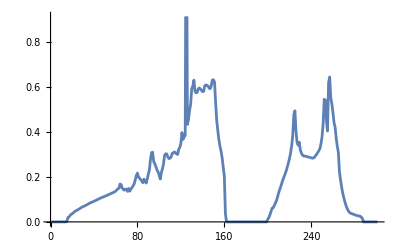

```mathematica
ListLinePlot[#2&@@@(cc2-dosc2a)]
```

```mathematica
Select[cc2d,0<#[[1]]<20&&#[[2]]<0.001&]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/dos.pdf",dplot]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/dos.pdf

```mathematica
Around[3.57,0.3 3.57]
```

3.61.1

```mathematica
Subdivide[3.57-]
```

Subdivide::sdmint: The number of subdivisions given in position 1 of Subdivide[0.714] should be a positive machine-sized integer.

Subdivide[0.714]

```mathematica
Subdivide[3.6-1.1,3.6+1.1,25]
```

{2.5,2.588,2.676,2.764,2.852,2.94,3.028,3.116,3.204,3.292,3.38,3.468,3.556,3.644,3.732,3.82,3.908,3.996,4.084,4.172,4.26,4.348,4.436,4.524,4.612,4.7}

```mathematica
2.956-2.90
```

0.056

## Diamond

```mathematica
dat2d=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/diamond/out.txt","Table"]//Flatten;
dat2d=dat2d[[1;;All]]
```

{-18.1628,-18.188,-18.1942,-18.1959,-18.1965,-18.1969,-18.197,-18.1968,-18.1968,-18.1968,-18.1969,-18.1972,-18.1966,-18.1969,-18.1968,-18.1969,-18.1969,-18.197,-18.1968,-18.1968,-18.1969,-18.1968,-18.1969,-18.1968,-18.1969,-18.1969}

```mathematica
dattr2d=Transpose[{Range[5,30,1],dat2d}];
```

```mathematica
fnfit2d=Interpolation[dattr2d,Method->"Spline",InterpolationOrder->6]
```

InterpolatingFunction[…]

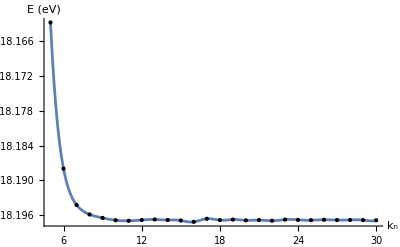

```mathematica
plt2d=Plot[fnfit2d[x],{x,5,30},Epilog->{Point[dattr2d]},PlotRange->All,AxesLabel->{"k_n","E (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltKdiamond.pdf",plt2d]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltKdiamond.pdf

```mathematica
douten=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/diamond/outen.txt","Table"]//Flatten;
```

```mathematica
vv=Transpose[{Range[2.5,4.7,0.088],douten}]
```

{{2.5,12.5987},{2.588,5.68884},{2.676,0.0681019},{2.764,-4.46853},{2.852,-8.102},{2.94,-10.9841},{3.028,-13.2346},{3.116,-14.9474},{3.204,-16.2246},{3.292,-17.1313},{3.38,-17.7288},{3.468,-18.0671},{3.556,-18.1935},{3.644,-18.1417},{3.732,-17.9505},{3.82,-17.6446},{3.908,-17.2487},{3.996,-16.7813},{4.084,-16.2598},{4.172,-15.6992},{4.26,-15.1107},{4.348,-14.5124},{4.436,-13.9112},{4.524,-13.3148},{4.612,-12.7281},{4.7,-12.1573}}

```mathematica
vv//Length
```

26

```mathematica
fnfit2d2=Interpolation[vv,Method->"Spline",InterpolationOrder->6]
```

InterpolatingFunction[…]

14.8164-12.3878 x+1.97509 x^2

216.847-132.807 x+18.7554 x^2

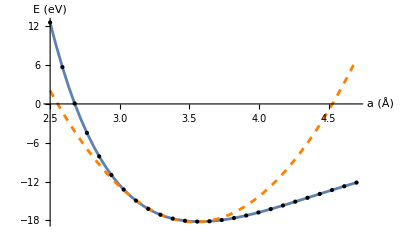

```mathematica
pf2=Fit[Take[vv,{7,-13}],{1,x,x^2},x]
ddds=Show[Plot[{fnfit2d2[x]},{x,2.5,4.7},PlotRange->All,AxesLabel->{"a (Å)","E (eV)"},Epilog->{Point[vv]}],Plot[pf2,{x,2.5,4.7},PlotStyle->{Dashed,Orange}],PlotRange->Automatic]
```

```mathematica
FindMinimum[pf2,{x,3.5}]
```

{-18.2555,{x→3.5405}}

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltEndiamond.pdf",ddds]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltEndiamond.pdf

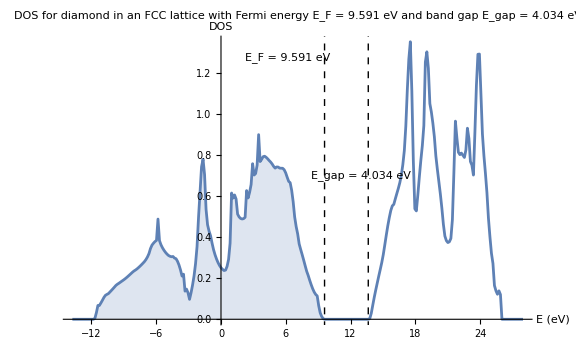

```mathematica
doscsd=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/diamond/Diamond/DOS/DOSCAR","Table","HeaderLines"->6];
cc2d={#1,#2}&@@@doscsd;
dplot=Show[ListLinePlot[cc2d,PlotRange->Automatic,ImageSize->Medium,AxesLabel->{"E (eV)","DOS"},Epilog->{Dashed,Line[{{9.591,-3},{9.591,3}}],Text["E_F = 9.591 eV",{6.15,1.275}],Text["E_gap = 4.034 eV",{13,0.7}],Dashed,Line[{{13.64,-3},{13.64,3}}]},PlotLabel->"DOS for diamond in an FCC lattice with Fermi energy E_F = 9.591 eV and band gap E_gap = 4.034 eV"],ListLinePlot[Select[cc2d,#[[1]]<=9.591&],Filling->Axis,PlotStyle->Directive[RGBColor[0,0,0,0.0]]],ImageSize->Large]
```

```mathematica
Select[cc2d,0<#[[1]]<20&&#[[2]]<0.001&]
```

{{9.606,0.},{9.745,0.},{9.885,0.},{10.024,0.},{10.163,0.},{10.302,0.},{10.441,0.},{10.58,0.},{10.719,0.},{10.858,0.},{10.997,0.},{11.137,0.},{11.276,0.},{11.415,0.},{11.554,0.},{11.693,0.},{11.832,0.},{11.971,0.},{12.11,0.},{12.249,0.},{12.388,0.},{12.528,0.},{12.667,0.},{12.806,0.},{12.945,0.},{13.084,0.},{13.223,0.},{13.362,0.},{13.501,0.},{13.64,0.}}

```mathematica
13.64- 9.606
```

4.034

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/dosdiamond.pdf",dplot]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/dosdiamond.pdf

```mathematica
Select[cc2d,9.59<#[[1]]<13.7&]
```

{{9.606,0.},{9.745,0.},{9.885,0.},{10.024,0.},{10.163,0.},{10.302,0.},{10.441,0.},{10.58,0.},{10.719,0.},{10.858,0.},{10.997,0.},{11.137,0.},{11.276,0.},{11.415,0.},{11.554,0.},{11.693,0.},{11.832,0.},{11.971,0.},{12.11,0.},{12.249,0.},{12.388,0.},{12.528,0.},{12.667,0.},{12.806,0.},{12.945,0.},{13.084,0.},{13.223,0.},{13.362,0.},{13.501,0.},{13.64,0.}}

```mathematica
bg=13.64-9.606
```

4.034

## Band structure diamond

```mathematica
bdumts=Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/diamond/bands/band_``.tsv",#],"Table","HeaderLines"->1]&/@Range[1,8]
```

```mathematica
bd1=bdumts[[1]];
bd2=bdumts[[2]];
```

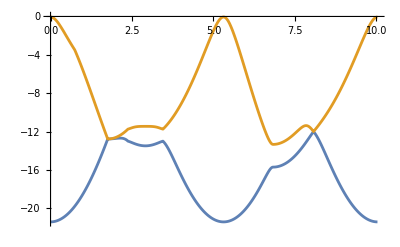

```mathematica
ListLinePlot[{bd1,bd2}]
```

```mathematica
Length@bdumts[[1]]
```

896

```mathematica
896/128
```

7

```mathematica
Last[bdumts[[1]]][[1]]
```

10.0351

```mathematica
#[[1]]&/@bdumts[[1]];
```

```mathematica
l={0}~Join~(#[[1]]&/@bdumts[[1]])[[128;;;;128]]
```

{0,1.75508,2.37559,3.45036,5.3119,6.83184,8.07287,10.0351}

```mathematica
{"Γ","X","U","K","Γ","L","W","X"}//Length
```

8

```mathematica
dd={#1,#2}&@@@Transpose[{l,{"Γ","X","U","K","Γ","L","W","X"}}]
```

{{0,Γ},{1.75508,X},{2.37559,U},{3.45036,K},{5.3119,Γ},{6.83184,L},{8.07287,W},{10.0351,X}}

```mathematica
bgpl=ListLinePlot[bdumts,PlotLabels->Evaluate[ToString@StringForm["Band ``",#]&/@Range[1,8]],ImageSize->Large,PlotLabel->"Energy bands for the diamond with band gap energy E_gap = 4.081 eV",Ticks->{dd,Automatic},Epilog->{{Arrowheads[{-.015,.015}],Arrow[{{5.3119,-0.022},{5.3119,5.49958}}]},Text["E_Γ = 5.555 eV",{6.25,2.15}],Text["E_gap = 4.081 eV",{2.25,2.00}],{Arrowheads[{-.015,.015}],Arrow[{{1.2714,-0.022},{1.2714,4.02641}}]}},AxesLabel->{"","E (eV)"}]
```

-Graphics-

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/bandsDiamond.pdf",bgpl]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/bandsDiamond.pdf

```mathematica
cm=MinimalBy[bdumts[[5]],#[[1]]>3&&#[[2]]&][[1]]
```

{5.3119,5.49958}

```mathematica
vm=MaximalBy[bdumts[[4]],#[[2]]&][[1]][[2]]
```

-0.055323

```mathematica
cm-vm
```

5.5549

```mathematica
cm1=MinimalBy[bdumts[[5]],#[[2]]&][[1]]
```

{1.2714,4.02641}

```mathematica
cm1-vm
```

4.08173

```mathematica
douteng=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/graphite/outen.txt","Table"]//Flatten;
```

```mathematica
vvg=Transpose[{Range[2.35,2.75,0.01],douteng}]
```

{{2.35,-36.0709},{2.36,-36.1903},{2.37,-36.2973},{2.38,-36.3925},{2.39,-36.4762},{2.4,-36.5483},{2.41,-36.6092},{2.42,-36.6594},{2.43,-36.6996},{2.44,-36.7296},{2.45,-36.7496},{2.46,-36.7601},{2.47,-36.7619},{2.48,-36.7548},{2.49,-36.7387},{2.5,-36.7144},{2.51,-36.6821},{2.52,-36.6422},{2.53,-36.5945},{2.54,-36.5391},{2.55,-36.4771},{2.56,-36.4031},{2.57,-36.3276},{2.58,-36.2456},{2.59,-36.1577},{2.6,-36.0637},{2.61,-35.9635},{2.62,-35.8578},{2.63,-35.7468},{2.64,-35.6313},{2.65,-35.5102},{2.66,-35.3847},{2.67,-35.2542},{2.68,-35.1195},{2.69,-34.9801},{2.7,-34.8362},{2.71,-34.6897},{2.72,-34.5385},{2.73,-34.3839},{2.74,-34.2259},{2.75,-34.0647}}

```mathematica
fnfit2d2g=Interpolation[vvg,Method->"Spline",InterpolationOrder->6]
```

InterpolatingFunction[…]

245.345-228.436 x+46.2433 x^2

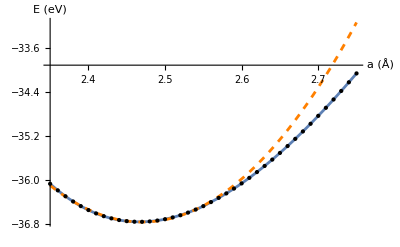

```mathematica
pf2g=Fit[Take[vvg,{2,-20}],{1,x,x^2},x]
dddsg=Show[Plot[{fnfit2d2g[x]},{x,2.35,2.75},PlotRange->All,AxesLabel->{"a (Å)","E (eV)"},Epilog->{Point[vvg]}],Plot[pf2g,{x,2.35,2.75},PlotStyle->{Dashed,Orange}],PlotRange->Automatic]
```

```mathematica
FindMinimum[pf2g,{x,2.5}]
```

{-36.7656,{x→2.46994}}

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltEngraphite.pdf",dddsg]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltEngraphite.pdf

```mathematica
dat2g=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/graphite/out.txt","Table"]//Flatten;
dat2g=dat2g[[1;;All]]
```

{-36.8293,-36.7888,-36.8824,-36.8663,-36.8444,-36.8684,-36.866,-36.8567,-36.8646,-36.8646,-36.8602,-36.8633,-36.8642,-36.8617,-36.8631,-36.8638,-36.8623,-36.8631,-36.8635,-36.8628,-36.863,-36.8634,-36.8629,-36.8629,-36.8634,-36.863}

```mathematica
dattr2g=Transpose[{Range[5,30,1],dat2g}];
```

```mathematica
fnfit2g=Interpolation[dattr2g,Method->"Spline",InterpolationOrder->6]
```

InterpolatingFunction[…]

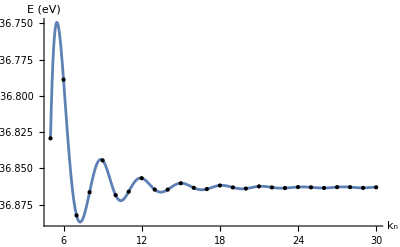

```mathematica
plt2g=Plot[fnfit2g[x],{x,5,30},Epilog->{Point[dattr2g]},PlotRange->All,AxesLabel->{"k_n","E (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltKgraphite.pdf",plt2g]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/freeenpltKgraphite.pdf

{0.0404447,0.0935478,0.0160246,0.0218984,0.0239596,0.00241245,0.00930423,0.00786766,3.88×10^-6,0.00438939,0.0031639,0.00086398,0.00246745,0.00133731,0.00077527,0.00149935,0.00071509,0.00043383,0.00067244,0.00016367,0.00044582,0.00056364,9.1×10^-7,0.00049464,0.00038494}

25

{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

25

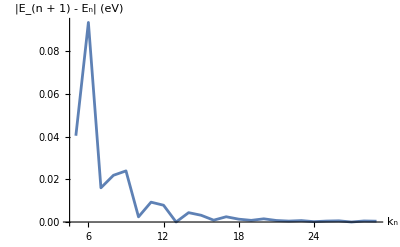

```mathematica
fg=Abs@Differences[dat2g]
Length@fg
Range[5,29]
Length@Range[5,29]
kpltConvg=ListLinePlot[Transpose[{Range[5,29],fg}],PlotRange->All,AxesLabel->{"k_n","|E_(n + 1) - E_n| (eV)"}]
```

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/kpltConvgraphite.pdf",kpltConvg]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/kpltConvgraphite.pdf

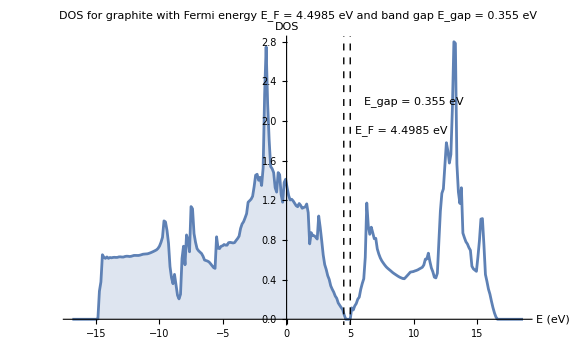

```mathematica
doscsg=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Cluster data/P4/graphite/DOSCAR","Table","HeaderLines"->6];
cc2g={#1,#2}&@@@doscsg;
dplotg=Show[ListLinePlot[{cc2g},PlotRange->All,ImageSize->Medium,AxesLabel->{"E (eV)","DOS"},Epilog->{Dashed,Line[{{4.4985,-3},{4.4985,3}}],Text["E_F = 4.4985 eV",{9,1.9}],Text["E_gap = 0.355 eV",{10,2.2}],Dashed,Line[{{5.008,-3},{5.008,3}}]},PlotLabel->"DOS for graphite with Fermi energy E_F = 4.4985 eV and band gap E_gap = 0.355 eV"],ListLinePlot[Select[cc2g,#[[1]]<=4.4985&],Filling->Axis,PlotStyle->Directive[RGBColor[0,0,0,0.0]]],ImageSize->Large]
```

```mathematica
Select[cc2g,0<#[[1]]<10&&#[[2]]<0.01&]
```

{{4.653,0.},{4.771,0.},{4.889,0.},{5.008,0.}}

```mathematica
5.008-4.653
```

0.355

```mathematica
Export["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/graphitedos.pdf",dplotg]
```

/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Computational material physics /Lab reports/4/graphitedos.pdf

```mathematica
Export["~/Downloads/datdoscgraph.tsv",cc2g]
```

~/Downloads/datdosc.tsv

```mathematica
cc2g//Short
```

{{-16.851,0.},{-16.733,0.},{-16.615,0.},{-16.497,0.},«294»,{18.359,0.},{18.477,0.},{18.596,0.}}

```mathematica
Pairwi
```